3.58504+1.89558 C+0.0261217 C^2-0.000259501 C^3

0.999606

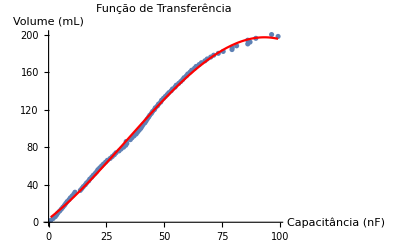

/Users/Rogiel/Documents/GitHub/ufrgs-instrumentacao-projeto/Resources/Mathematica/Images/Nivel/TransferFunctionPlot.pdf

```mathematica
data={{2,0.92},{4,1.95},{6,2.9},{8,3.5},{10,4.02},{12,4.8},{14,5.5},{16,6.16},{18,6.84},{20,7.41},{22,8.01},{24,8.82},{26,9.4},{28,10.18},{30,10.9},{32,11.4},{34,13.71},{36,14.39},{38,15.02},{40,15.84},{42,16.42},{44,17.28},{46,17.79},{48,18.61},{50,19.28},{52,20.1},{54,20.8},{56,21.3},{58,22.1},{60,22.9},{62,23.7},{64,24.6},{66,25.4},{68,26.6},{70,27.5},{72,28.4},{74,29.1},{76,30.4},{78,31.3},{80,32.4},{82,33.3},{84,33.8},{86,33.5},{88,35.3},{90,36},{92,36.9},{94,37.8},{96,38.4},{98,39.1},{100,39.8},{102,40.3},{104,40.8},{106,41.6},{108,42.1},{110,42.6},{112,43.2},{114,43.7},{116,44.4},{118,44.9},{120,45.7},{122,46.1},{124,47},{126,47.5},{128,48.4},{130,48.8},{132,49.6},{134,50.4},{136,51.2},{138,51.9},{140,52.9},{142,53.5},{144,54.6},{146,55.1},{148,56.2},{150,57.1},{152,57.9},{154,58.5},{156,59.5},{158,60.1},{160,61.1},{162,61.8},{164,63},{166,63.7},{168,65},{170,66},{172,67.5},{174,68.5},{176,70},{178,71.3},{180,73.3},{182,75.4},{184,79.2},{186,79.3},{188,81.2},{190,86},{192,87},{194,86},{196,89.5},
{198,99.1},{200,96.3}};
data=Reverse/@data;

model=NonlinearModelFit[data, a+b*C+c Power[C, 2]+d Power[C, 3], {a,b,c,d}, {C}];
Normal[model]
model["RSquared"]

tf=Show[
ListPlot[data],
Plot[model[h], {h, Min[data[[All, 1]]],Max[data[[All, 1]]]}, PlotStyle->Red],
AxesLabel->{ "Capacitância (nF)","Volume (mL)"},
PlotLabel->"Função de Transferência"
]
Export[NotebookDirectory[]<>"Images/Nivel/TransferFunctionPlot.pdf", tf]
```